```mathematica
ic=Table[{a=1+k,b=1+l},{k,-0.5,0.5,0.2},{l,-0.5,0.5,0.2}]
```

{{{0.5,0.5},{0.5,0.7},{0.5,0.9},{0.5,1.1},{0.5,1.3},{0.5,1.5}},{{0.7,0.5},{0.7,0.7},{0.7,0.9},{0.7,1.1},{0.7,1.3},{0.7,1.5}},{{0.9,0.5},{0.9,0.7},{0.9,0.9},{0.9,1.1},{0.9,1.3},{0.9,1.5}},{{1.1,0.5},{1.1,0.7},{1.1,0.9},{1.1,1.1},{1.1,1.3},{1.1,1.5}},{{1.3,0.5},{1.3,0.7},{1.3,0.9},{1.3,1.1},{1.3,1.3},{1.3,1.5}},{{1.5,0.5},{1.5,0.7},{1.5,0.9},{1.5,1.1},{1.5,1.3},{1.5,1.5}}}

```mathematica
ic=Flatten[ic,1]
```

{{0.5,0.5},{0.5,0.7},{0.5,0.9},{0.5,1.1},{0.5,1.3},{0.5,1.5},{0.7,0.5},{0.7,0.7},{0.7,0.9},{0.7,1.1},{0.7,1.3},{0.7,1.5},{0.9,0.5},{0.9,0.7},{0.9,0.9},{0.9,1.1},{0.9,1.3},{0.9,1.5},{1.1,0.5},{1.1,0.7},{1.1,0.9},{1.1,1.1},{1.1,1.3},{1.1,1.5},{1.3,0.5},{1.3,0.7},{1.3,0.9},{1.3,1.1},{1.3,1.3},{1.3,1.5},{1.5,0.5},{1.5,0.7},{1.5,0.9},{1.5,1.1},{1.5,1.3},{1.5,1.5}}

Table::itraw: Raw object 1 cannot be used as an iterator.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[Visualization`Utilities`ScaleCatPlotRange[ListPlot,#1,#2]&,{{{4,4}},{{Identity,Identity},{Identity,Identity}}}]; dimensions are 1 and 2.

ListPlot::prng: Value of option PlotRange -> MapThread[Visualization`Utilities`ScaleCatPlotRange[ListPlot,#1,#2]&,{{{4,4}},{{Identity,Identity},{Identity,Identity}}}] is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

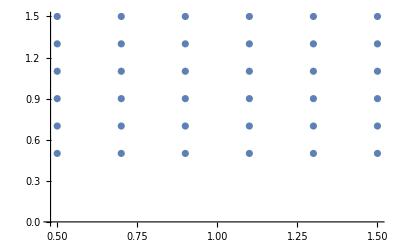

```mathematica
ListPlot[ic,PlotRange->{{-2,2}{-2,2}},PlotStyle->Dashed]
```

```mathematica
deq=x''[t]+ω^2 x[t]==0
f1=x'[t]==p[t]
f2=p'[t]==-ω^2 x[t]
```

ω^2 x[t]+x''[t]==0

x'[t]==p[t]

p'[t]==-ω^2 x[t]

```mathematica
sol=DSolve[{f1,f2,x[0]==x0,p[0]==p0},{x,p},t]
```

{{p→Function[{t},p0 Cos[t ω]-x0 ω Sin[t ω]],x→Function[{t},(x0 ω Cos[t ω]+p0 Sin[t ω])/ω]}}

```mathematica
xx[t]=x[t]/.sol[[1]];
pp[t]=p[t]/.sol[[1]];
Print["x[t]=",xx[t]]
Print["p[t]=",pp[t]]
```

x[t]=(x0 ω Cos[t ω]+p0 Sin[t ω])/ω

p[t]=p0 Cos[t ω]-x0 ω Sin[t ω]

1/2

0.5 Cos[t/2]

-0.25 Sin[t/2]

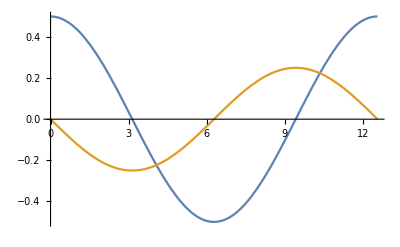

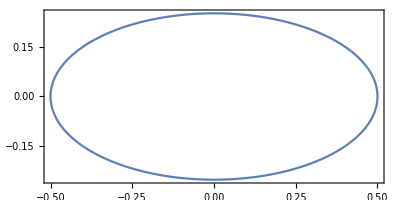

```mathematica
ω=1/2
x1[t_]=xx[t]/.x0->0.5/.p0->0
p1[t_]=pp[t]/.x0->0.5/.p0->0
T=2Pi/ω;
Plot[{x1[t],p1[t]},{t,0,T}]
ParametricPlot[{x1[t],p1[t]},{t,0,T},Frame->True]
```

## Δυναμικό και ενέργεια

```mathematica
Remove[x,p,ω];
U[x_]=∫ω^2ⅆx
gr1=Plot[U[x],{x,-2,3}]
```

```mathematica
eqpoints=NSolve[f[x]==0,x]
```

## Σημεία Ισορροπίας

```mathematica
x01=x/.eqpoints[[1]]
x02=x/.eqpoints[[2]]
E1=Energy[x01,0]
E2=Energy[x02,0]
Plot[{U[x],E1,E2},{x,-1.5,2.5},AxesLabel->{"x","U[x]"}]
```